## Fit student correctness to various models

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/bvds/Andes2/LogProcessing/moment-of-learning

```mathematica
data=Import["junk.csv"];
```

```mathematica
Take[data,5]
```

{{accel-constant-speed,asu_9Q1920841f2ca4d1fasul1_c,md5:b50efcf571b671cf01b499841c66daf2,0},{area-of-circle,asu_9Q1920841f2ca4d1fasul1_c,md5:b50efcf571b671cf01b499841c66daf2,0,1},{bernoulli,asu_9Q1920841f2ca4d1fasul1_c,md5:b50efcf571b671cf01b499841c66daf2,0,0,1},{combo-magnification,asu_9Q1920841f2ca4d1fasul1_c,md5:b50efcf571b671cf01b499841c66daf2,0},{compo-general-case,asu_9Q1920841f2ca4d1fasul1_c,md5:b50efcf571b671cf01b499841c66daf2,1,0,0,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,0,0,1,1,1,1,1,1,1,1,1,1,1}}

```mathematica
logistic[n_,{mu_,b_}]:=1/(Exp[-b  n+mu]+1); (* this choice of parameters gives finite constraint region *)
step[n_,{nl_,pg_,ps_}]:=pg+(Sign[n-nl+1/2]+1) (1-ps-pg)/2;
bkt[n_,{b_,pg_,ps_}]:=1-ps-(1-ps-pg)*Exp[-b n]
```

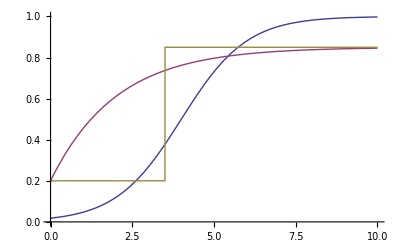

```mathematica
Plot[{logistic[x,{4,1}],bkt[x,{.5,.2,.15}],step[x,{4,.2,.15}]},{x,0,10},PlotRange->{0,1}]
```

```mathematica
logger[x_?NumberQ,params_]:= (* not used now. *)Which[0<x≤1,Log[x],x==0,(* NMaximize can't handle Infinity *)-10^50,True,Print["Invalid probability ",x," for ",params];If[x<0,-Infinity,0]]
logProb[model_,params_,data_]:=Sum[Log[If[data[[i]]==1,model[i,params],1-model[i,params]]],{i,Length[data]}]
maxer[model_,vars_,constraints_,data_]:=Map[{Print[#[[1]]];#[[1]],Which[
(* too few data points *)
Length[Drop[#,3]]<Length[vars],Null,
(* All three functions can perfectly fit to all ones or zeros, but numerical fit is hard. *)
Count[Drop[#,3],0]==0 || Count[Drop[#,3],1]==0,2 Length[vars],True,
Block[{x=NMaximize[{logProb[model,vars,Drop[#,3]],constraints[Drop[#,3]]},vars,Method->{"RandomSearch",Method->"ConjugateGradient"}]},If[NumberQ[x[[1]]],2Length[vars]-2 x[[1]],Print[#,x];False]]]}&,data]
```

```mathematica
data[[11]]
```

{continuity,asu_9Q1920841f2ca4d1fasul1_c,md5:b50efcf571b671cf01b499841c66daf2,1,0}

```mathematica
logisticConstraints[x_]:=Block[{delta=15,ones=Position[x,1,1],zeros=Position[x,0,1]},mu≥Max[zeros[[-1,1]]*b,zeros[[1,1]]*b]-delta&& mu≤Min[ones[[1,1]]*b,ones[[-1,1]]*b]+delta&& b>-2 delta/Max[1,ones[[-1,1]]-zeros[[1,1]]] && b<2 delta/Max[1,zeros[[-1,1]]-ones[[1,1]]]]
```

```mathematica
TableForm[maxer[logistic,{mu,b},logisticConstraints,data[[{11}]]]]
```

continuity

Experimental`NumericalFunction::nnum: The function value Indeterminate is not a number at {b, mu} = {-30.`, -238.91599470221024`}.

General::stop: Further output of Experimental`NumericalFunction will be suppressed during this calculation.

continuity | 4.

```mathematica
TableForm[maxer[logistic,{mu,b},logisticConstraints,data]]
```

accel-constant-speed

area-of-circle

bernoulli

combo-magnification

compo-general-case

compo-general-case-unknown

compo-parallel-axis

compo-perpendicular

compo-z-axis

compo-zero-vector

continuity

Experimental`NumericalFunction::nnum: The function value Indeterminate is not a number at {b, mu} = {-30.`, -238.91599470221024`}.

General::stop: Further output of Experimental`NumericalFunction will be suppressed during this calculation.

define-angle-between-lines

define-angular-frequency

define-area

define-area-at

define-charge

define-coef-friction

define-compression

define-current-thru

define-distance

define-distance-between

define-duration

define-electric-power-var

define-energy-var

define-flux

define-focal-length

define-frequency

define-grav-accel

define-image-distance

define-index-of-refraction

define-magnification

define-mass

define-mass-density

define-moment-of-inertia

define-object-distance

define-period-var

define-pressure

define-radius-of-circle

define-resistance-var

define-revolution-radius

define-shape-length

define-slit-separation

define-speed

define-spring-constant

define-stored-energy-var

define-turns

define-voltage-across

define-volume

define-wavelength

define-work

definition-syntax

draw-accel-free-fall

draw-accel-slow-down

draw-accel-speed-up

draw-ang-accel

draw-ang-accel-speed-up

draw-ang-displacement-unknown

draw-ang-momentum-rotating

draw-ang-velocity-rotating

draw-applied-force

draw-bfield-straight-current

draw-bforce-charge

draw-bforce-rhr-zero

draw-bforce-unknown-velocity

draw-body

draw-buoyant-force

draw-centripetal-acceleration

draw-compo-form-axes

draw-coulomb-force-unknown

draw-displacement-given-dir

draw-displacement-straight

draw-displacement-unknown

draw-displacement-zero

draw-electric-force-given-field-dir

draw-electric-force-given-field-unknown

draw-energy-axes

draw-field-given-dir

draw-field-unknown

draw-grav-force

draw-impulse-given-momenta

draw-kinetic-friction

draw-line-given-dir

draw-line-unknown-dir

draw-momentum-at-rest

draw-momentum-straight

draw-net-field-given-dir

draw-net-field-given-zero

draw-net-field-unknown

draw-net-force-from-accel

draw-net-force-from-forces

draw-net-force-unknown

draw-normal

draw-point-efield-unknown

draw-projection-axes

draw-relative-position

draw-relative-position-unknown

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

draw-spring-force

draw-tension

draw-torque

draw-unrotated-axes

draw-vector-aligned-axes

draw-velocity-at-rest

draw-velocity-curved

draw-velocity-curved-unknown

draw-velocity-momentarily-at-rest

draw-velocity-straight

draw-velocity-straight-unknown

draw-weight

draw-xy-vector-given-compos

draw-z-axis-vector-given-compos

equation-syntax

equiv-resistance-parallel

equiv-resistance-series

kinetic-friction-law

lens-combo

lens-eqn

magnification-eqn

object-label

pendulum-oscillation

pressure-at-open-to-atmosphere

pressure-force

pressure-height-fluid

sdd-constvel-compo

select-mc-answer

spring-law-compression

spring-mass-oscillation

write-ang-momentum

write-angle-direction-known-lines

write-archimedes

write-average-rate-of-change

write-cap-energy

write-capacitance-definition

write-centripetal-accel

write-change-me

write-charge-force-bfield

write-charge-force-bfield-mag

write-charge-force-efield-compo

write-charge-force-efield-mag

write-charge-same-caps-in-branch

write-connected-accels

write-cons-angmom

write-cons-linmom-compo-join-split

write-coulomb

write-coulomb-compo

write-density

write-electric-power

write-energy-cons

write-equality

write-faradays-law

write-flux-constant-field

write-flux-zero

write-free-fall-accel

write-g-on-earth

write-grav-energy

write-harmonic-of

write-height-dy

write-i-hoop-cm

write-impulse-compo

write-impulse-momentum-compo

write-inside-solenoid-bfield

write-junction-rule

write-junction-rule-cap

write-kinetic-energy

write-known-value-eqn

write-linear-vel

write-lk-no-s-compo

write-lk-no-t-compo

write-lk-no-vf-compo

write-loop-rule-capacitors

write-loop-rule-resistors

write-mag-torque

write-mass-compound

write-momentum-compo

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

write-net-field-compo

write-net-force-compo

write-nfl-compo

write-nsl-compo

write-nsl-rot-compo

write-null-spring-energy

write-ohms-law

write-period-circular

write-point-charge-efield-compo

write-potential-energy

write-right-triangle-tangent

write-rk-no-s

write-rk-no-vf

write-sdd

write-single-loop-rule

write-slit-interference

write-snells-law

write-spring-energy

write-straight-wire-bfield

write-sum-disp-compo

write-sum-times

write-tensions-equal

write-total-energy-top

write-transformer-power

write-turns-per-length

write-ug

write-unit-vector-mag

write-vector-magnitude

write-wave-speed-light

write-wnc

write-work

wt-law

accel-constant-speed | Null
area-of-circle | 4.
bernoulli | 4.00003
combo-magnification | Null
compo-general-case | 33.8361
compo-general-case-unknown | Null
compo-parallel-axis | 83.8958
compo-perpendicular | 41.5199
compo-z-axis | 16.891
compo-zero-vector | Null
continuity | 4.
define-angle-between-lines | 4
define-angular-frequency | 8.69497
define-area | Null
define-area-at | 4
define-charge | 29.0253
define-coef-friction | Null
define-compression | 4
define-current-thru | 17.6094
define-distance | 4.
define-distance-between | 10.5404
define-duration | 22.6107
define-electric-power-var | 4.
define-energy-var | Null
define-flux | 4.
define-focal-length | 4.
define-frequency | 22.5724
define-grav-accel | 4
define-image-distance | 8.22397
define-index-of-refraction | 4
define-magnification | 4.
define-mass | 18.2314
define-mass-density | 4.
define-moment-of-inertia | 4.
define-object-distance | 4.
define-period-var | 8.22397
define-pressure | 15.8216
define-radius-of-circle | 4.
define-resistance-var | 15.5238
define-revolution-radius | 4
define-shape-length | 4.
define-slit-separation | 4.
define-speed | 8.33081
define-spring-constant | 7.81909
define-stored-energy-var | 4
define-turns | 4
define-voltage-across | 23.6526
define-volume | Null
define-wavelength | 4.
define-work | 7.81909
definition-syntax | 4
draw-accel-free-fall | 4
draw-accel-slow-down | Null
draw-accel-speed-up | 14.7537
draw-ang-accel | Null
draw-ang-accel-speed-up | 4.
draw-ang-displacement-unknown | Null
draw-ang-momentum-rotating | 4
draw-ang-velocity-rotating | 4.
draw-applied-force | 4.
draw-bfield-straight-current | 8.22397
draw-bforce-charge | 4.
draw-bforce-rhr-zero | Null
draw-bforce-unknown-velocity | Null
draw-body | 65.2013
draw-buoyant-force | Null
draw-centripetal-acceleration | 8.22397
draw-compo-form-axes | 17.9209
draw-coulomb-force-unknown | 4.00003
draw-displacement-given-dir | 8.33081
draw-displacement-straight | 10.3024
draw-displacement-unknown | Null
draw-displacement-zero | Null
draw-electric-force-given-field-dir | Null
draw-electric-force-given-field-unknown | Null
draw-energy-axes | 4.
draw-field-given-dir | 9.30275
draw-field-unknown | Null
draw-grav-force | 4
draw-impulse-given-momenta | Null
draw-kinetic-friction | 4
draw-line-given-dir | 14.7039
draw-line-unknown-dir | 4
draw-momentum-at-rest | 4
draw-momentum-straight | 12.8695
draw-net-field-given-dir | 4
draw-net-field-given-zero | Null
draw-net-field-unknown | Null
draw-net-force-from-accel | 4.
draw-net-force-from-forces | Null
draw-net-force-unknown | Null
draw-normal | 10.7728
draw-point-efield-unknown | 4.
draw-projection-axes | 4
draw-relative-position | 8.36664
draw-relative-position-unknown | 4.
draw-spring-force | 4.
draw-tension | 15.8515
draw-torque | Null
draw-unrotated-axes | 27.0241
draw-vector-aligned-axes | 4
draw-velocity-at-rest | 9.54518
draw-velocity-curved | 15.1537
draw-velocity-curved-unknown | 4
draw-velocity-momentarily-at-rest | 10.9233
draw-velocity-straight | 39.3697
draw-velocity-straight-unknown | Null
draw-weight | 18.5417
draw-xy-vector-given-compos | 4.
draw-z-axis-vector-given-compos | 4.
equation-syntax | 30.9886
equiv-resistance-parallel | 9.54518
equiv-resistance-series | 4
kinetic-friction-law | Null
lens-combo | Null
lens-eqn | 8.69497
magnification-eqn | 4
object-label | 4
pendulum-oscillation | 4.
pressure-at-open-to-atmosphere | 4.
pressure-force | 4.
pressure-height-fluid | Null
sdd-constvel-compo | 9.54518
select-mc-answer | 71.2864
spring-law-compression | 4.
spring-mass-oscillation | Null
write-ang-momentum | 4.
write-angle-direction-known-lines | 4.00003
write-archimedes | Null
write-average-rate-of-change | Null
write-cap-energy | 4
write-capacitance-definition | 4.
write-centripetal-accel | 4.
write-change-me | Null
write-charge-force-bfield | 7.81909
write-charge-force-bfield-mag | 4.
write-charge-force-efield-compo | 4
write-charge-force-efield-mag | Null
write-charge-same-caps-in-branch | Null
write-connected-accels | 4.
write-cons-angmom | Null
write-cons-linmom-compo-join-split | 4
write-coulomb | Null
write-coulomb-compo | 4.
write-density | Null
write-electric-power | 8.22397
write-energy-cons | 4
write-equality | 4
write-faradays-law | Null
write-flux-constant-field | Null
write-flux-zero | Null
write-free-fall-accel | 4
write-g-on-earth | Null
write-grav-energy | 9.0061
write-harmonic-of | 4
write-height-dy | 4.
write-i-hoop-cm | Null
write-impulse-compo | Null
write-impulse-momentum-compo | Null
write-inside-solenoid-bfield | Null
write-junction-rule | Null
write-junction-rule-cap | Null
write-kinetic-energy | 16.3653
write-known-value-eqn | 239.584
write-linear-vel | Null
write-lk-no-s-compo | 14.3543
write-lk-no-t-compo | 4.
write-lk-no-vf-compo | 10.3024
write-loop-rule-capacitors | 12.4747
write-loop-rule-resistors | 10.7301
write-mag-torque | Null
write-mass-compound | Null
write-momentum-compo | 4.
write-net-field-compo | 4
write-net-force-compo | 10.5404
write-nfl-compo | 13.4378
write-nsl-compo | 21.9682
write-nsl-rot-compo | Null
write-null-spring-energy | Null
write-ohms-law | 16.7064
write-period-circular | Null
write-point-charge-efield-compo | 4.
write-potential-energy | Null
write-right-triangle-tangent | 4.
write-rk-no-s | 4
write-rk-no-vf | Null
write-sdd | 8.22397
write-single-loop-rule | Null
write-slit-interference | 4.
write-snells-law | Null
write-spring-energy | 8.22397
write-straight-wire-bfield | 4.
write-sum-disp-compo | 4
write-sum-times | 4.
write-tensions-equal | 4
write-total-energy-top | 15.0904
write-transformer-power | Null
write-turns-per-length | Null
write-ug | 4.
write-unit-vector-mag | Null
write-vector-magnitude | 4.
write-wave-speed-light | Null
write-wnc | Null
write-work | 4.
wt-law | 16.6067

```mathematica
logProb[bkt,{b,pg,ps},Drop[data[[3]],3]]
```

Log[1-ⅇ^(-3 b) (1-pg-ps)-ps]+Log[ⅇ^(-2 b) (1-pg-ps)+ps]+Log[ⅇ^-b (1-pg-ps)+ps]

```mathematica
TableForm[maxer[bkt,{b,pg,ps},Block[{delta=15},pg≥Exp[-delta] && ps≥Exp[-delta] && pg≤1-Exp[-delta] && ps≤ 1-Exp[-delta] &&b≥0 && b<delta]&,Take[data,20]]]
```

accel-constant-speed

area-of-circle

bernoulli

combo-magnification

compo-general-case

compo-general-case-unknown

compo-parallel-axis

compo-perpendicular

compo-z-axis

compo-zero-vector

continuity

define-angle-between-lines

define-angular-frequency

define-area

define-area-at

define-charge

define-coef-friction

define-compression

define-current-thru

define-distance

accel-constant-speed | Null
area-of-circle | Null
bernoulli | 9.81884
combo-magnification | Null
compo-general-case | 38.0697
compo-general-case-unknown | Null
compo-parallel-axis | 86.2414
compo-perpendicular | 43.5205
compo-z-axis | 18.8908
compo-zero-vector | Null
continuity | Null
define-angle-between-lines | 6
define-angular-frequency | 10.7073
define-area | Null
define-area-at | Null
define-charge | 31.1273
define-coef-friction | Null
define-compression | Null
define-current-thru | 19.7861
define-distance | 11.5452

```mathematica
TableForm[maxer[step,{nl,pg,ps},Block[{delta=15},pg≥Exp[-delta] && ps≥ Exp[-delta] && pg≤1-Exp[-delta] && ps≤1-Exp[-delta] &&Element[nl,Integers]&&
	nl≤Length[#] && nl≥1]&,Take[data,20]]]
```

accel-constant-speed

area-of-circle

bernoulli

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

combo-magnification

compo-general-case

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

compo-general-case-unknown

compo-parallel-axis

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMaximize will be suppressed during this calculation.

compo-perpendicular

compo-z-axis

compo-zero-vector

continuity

define-angle-between-lines

define-angular-frequency

define-area

define-area-at

define-charge

define-coef-friction

define-compression

define-current-thru

define-distance

accel-constant-speed | Null
area-of-circle | Null
bernoulli | 6.
combo-magnification | Null
compo-general-case | 38.5055
compo-general-case-unknown | Null
compo-parallel-axis | 86.3792
compo-perpendicular | 43.0229
compo-z-axis | 18.9481
compo-zero-vector | Null
continuity | Null
define-angle-between-lines | 6
define-angular-frequency | 9.94513
define-area | Null
define-area-at | Null
define-charge | 30.2123
define-coef-friction | Null
define-compression | Null
define-current-thru | 21.293
define-distance | 6.